```mathematica
f[x_,u_,s_]:=Exp[-(x-u)^2/(2*s^2)]/(Sqrt[2*Pi]*s)
```

```mathematica
f[1,1,1]
```

1/(2 π Sqrt)

```mathematica
g1[x_]:=0.9*f[x,0,1]
```

```mathematica
g2[x_]:=0.1*f[x,3,Sqrt[3]]

Solve[g1[x]==g2[x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
{{x->-5.3716394673330345},{x->2.3716394673330345}}

Solve[-x^2/2+Log[0.9]==-(x-3)^2/6-Log[Sqrt[3]]+Log[0.1]]
```

{{x→-5.37164},{x→2.37164}}

{{x→-5.37164},{x→2.37164}}

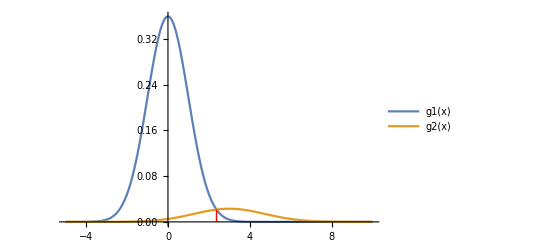

```mathematica
Plot[{g1[x],g2[x]},{x,-5,10},PlotLegends->"Expressions",Epilog->{Red,Line[{{2.37164,0},{2.37164,g1[2.37164]}}]},PlotRange->Full]
```

```mathematica
Solve[g1[x]==g2[x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-5.37164},{x→2.37164}}

```mathematica
sin(x)
```

sin x

```mathematica
Sin[3]
```

```mathematica
Sin[3.0]
```

0.14112

```mathematica
Pi
```

π